```mathematica
tf=Import["D:\\document\\work\\artivvis-development-repository\\Samples\\Tooth\\tooth.tfi","XML"];
bincount=256;
intensity=ToExpression@Cases[tf,XMLElement["intensity",{"value"->atrib_,___},___]:>atrib,∞];
r=ToExpression@Cases[tf,XMLElement["colorL",{"r"->atrib_,___},___]:>atrib,∞];
g=ToExpression@Cases[tf,XMLElement["colorL",{___,"g"->atrib_,___},___]:>atrib,∞];
b=ToExpression@Cases[tf,XMLElement["colorL",{___,"b"->atrib_,___},___]:>atrib,∞];
a=ToExpression@Cases[tf,XMLElement["colorL",{___,"a"->atrib_},___]:>atrib,∞];
rgbcolors=(#/255.&)/@Transpose[{r,g,b}]//(RGBColor/@#&);
rgbfunction=(Blend[Transpose[{intensity,rgbcolors}], #1] & );
rgba=(#/255.&)/@Transpose[{r,g,b,a}]//(RGBColor/@#&);
rgbafunction=(Blend[Transpose[{intensity,rgba}], #1] & );
alpha=(#/255.&)/@a;
rgbcolors
intensity
bincount=256;
```

{RGBColor[{0., 0.6666666666666666, 1.}],RGBColor[{0., 0.6666666666666666, 1.}],RGBColor[{0., 0.6666666666666666, 1.}],RGBColor[{1., 0., 0.}],RGBColor[{1., 0., 0.}],RGBColor[{1., 0., 0.}],RGBColor[{1., 1., 0.}],RGBColor[{1., 1., 0.}],RGBColor[{1., 1., 0.}]}

{0.04,0.28,0.5,0.58,0.64,0.7,0.76,0.88,1}

```mathematica
intensity
alpha
```

{0.04,0.28,0.5,0.58,0.64,0.7,0.76,0.88,1}

{0.,0.27451,0.,0.,0.27451,0.,0.,0.27451,0.}

```mathematica
rgbafunction[0.01]//InputForm
```

RGBColor[0., 0.6666666666666666, 1., 0.]

```mathematica
rgbafunction[0.06463879]//InputForm
```

RGBColor[0., 0.6666666666666666, 1., 0.028181622549019607]

```mathematica
d = Import["D:\\document\\work\\artivvis-development-repository\\Samples\\Tooth\\tooth.tif","Image3D"];
dtf=Image3D[d,ColorFunction->rgbafunction];
```

```mathematica
list=Reverse@Image3DSlices[d,All,2];
count=Length[list]
img=First[list];
list2=Table[img=ImageApply[#1+Clip[1-#1,{0,1}]*f[#2]&,{img,list[[i]]}],{i,2,count}]//Join[{First[list]},#]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,count}]//Join[{First[list]},#]&;
d5a=Image3D[list3];
d5=ImageRotate[d5a,{90 Degree,{1,0,0}}]
```

120

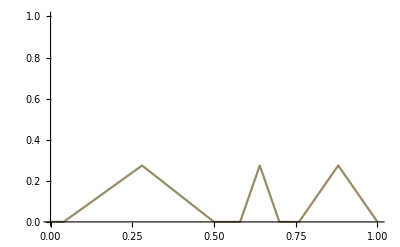

```mathematica
intensity0=intensity;
alpha0=alpha;
If[First[intensity0]>0,intensity0=Join[{0},intensity0];alpha0=Join[{0},alpha0]];
If[Last[intensity0]<1,intensity0=Join[intensity0,{1}];alpha0=Join[alpha0,{0}]];
(*ListLinePlot[Transpose[{intensity0,alpha0}],PlotRange->{{0,1},{0,1}},ColorFunction->rgbfunction,PlotLegends->"user specified transfer function"]*)
f=Interpolation[Transpose[{intensity0,alpha0}],InterpolationOrder->1];
Plot[f[x],{x,0,1},PlotRange->{{0,1},{0,1}},ColorFunction->rgbfunction,PlotLegends->"user specified transfer function"]
```

```mathematica
list4=Table[ImageApply[List@@rgbfunction[#]&,{list[[i]]}],{i,1,count}];
list5=Table[ImageApply[f[#]&,{list[[i]]}],{i,1,count}];
```

```mathematica
GaussianMatrix[1]
GaussianMatrix[1]//Total//Total
```

{{0.00987648,0.0796275,0.00987648},{0.0796275,0.641984,0.0796275},{0.00987648,0.0796275,0.00987648}}

1.

2

0.353553

{{2.97907×10^-6,0.0000953923,0.00152926,0.0000953923,2.97907×10^-6},{0.0000953923,0.00305454,0.048968,0.00305454,0.0000953923},{0.00152926,0.048968,0.785018,0.048968,0.00152926},{0.0000953923,0.00305454,0.048968,0.00305454,0.0000953923},{2.97907×10^-6,0.0000953923,0.00152926,0.0000953923,2.97907×10^-6}}

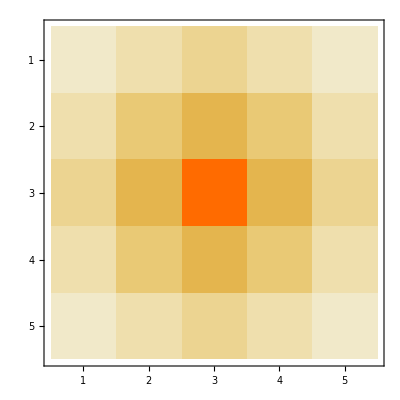

```mathematica
r=2
sigma=Sqrt[2]/8.*r
GaussianMatrix[{r,sigma}]
GaussianMatrix[{r,sigma}]//MatrixPlot
```

```mathematica
(*f1=ImageApply[If[#>0,#2,0]&,{feature, d5}]*)
```

```mathematica
bin=MorphologicalComponents[d]//Colorize[#]&;
distance=DistanceTransform[bin]//ImageAdjust;
zero=ImageResize[Image3D[ConstantArray[0,{1,1,1}]],ImageDimensions[d]];
com=ColorCombine[{ImageAdjust[d],distance,zero}];
```

```mathematica
(*MapIndexed[Export[NotebookDirectory[]<>"tooth\\"<>IntegerString[First[#2],10,3]<>".png",#]&,Image3DSlices[com]];*)
```

```mathematica
ClusteringComponents[com,3]//Colorize[#-1]&
ClusteringComponents[com,4]//Colorize[#-1]&
```

```mathematica
tr=Transpose[{Flatten@ImageData@ImageAdjust[d],Flatten@ImageData[distance]}];
ListPlot[tr,PlotRange->{{0,1},{0,1}}]
```

```mathematica
tr=Transpose[{Flatten@ImageData[d],Flatten@ImageData[distance]}];
ListPlot[tr,PlotRange->{{0,1},{0,1}}]
```

```mathematica
tr2=Transpose[{Flatten@ImageData[d],Flatten@ImageData[dog]}];
ListPlot[tr2,PlotRange->{{0,1},{0,1}}]
```

```mathematica
tr2=Transpose[{Flatten@ImageData[d],Flatten@ImageData[ImageAdjust[dog]]}];
ListPlot[tr2,PlotRange->{{0,1},{0,1}}]
```